```mathematica
norm[t_,a_]:=1/(√(2π))ⅇ^(-1/2(t-a)^2);
```

```mathematica
normInt=∫_(-∞)^x norm[t,a]ⅆt
```

1/2 Erfc[(a-x)/(√2)]

```mathematica
normIntEval[x_]:=1/2 (1+Erf[(3+x)/(√2)])
```

```mathematica
normSkew[a_,b_]:=(norm[x,a]normIntEval[b x])/normIntEval[0]
```

(ⅇ^(-x^2/2) (1+Erf[(3 x)/(√2)]))/(√(2 π))

```mathematica
normSkew[5,2]
```

(ⅇ^(-1/2 (-5+x)^2) (1+Erf[(3+2 x)/(√2)]))/(√(2 π) (1+Erf[3/(√2)]))

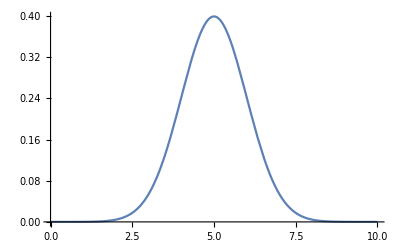

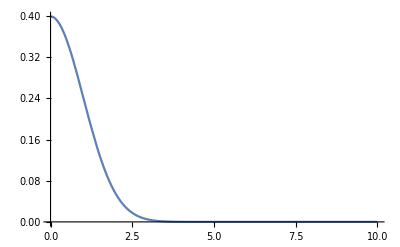

```mathematica
Plot[normSkew[5,10000000000],{x,0,10}, PlotRange->All]
Plot[norm[x,0],{x,0,10}, PlotRange->All]
```